{x→7.78375×10^-17}

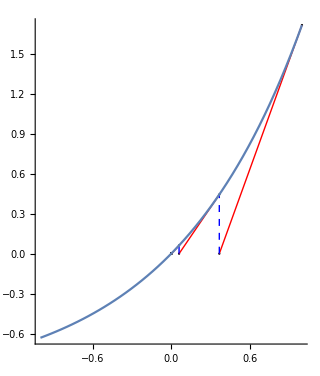

```mathematica
f[x_]:=Exp[x]-1;
Subscript[x, 0]=1;
{sol, step} = Reap[FindRoot[f[x],{x,Subscript[x, 0]},EvaluationMonitor:>Sow[x]]];
sol
data = Flatten[{{#,f[#]},{ #-f[#]/f'[#],0}}&/@Flatten[step],1];
Show[Graphics@GraphicsComplex[data, {PointSize[0.005],Point[data],Red, Line[Table[{i,i+1},{i,1,Length[data],2}]], Dashed,Blue, Line[Table[{i,i+1},{i,2,Length[data]-1,2}]] }],Plot[f[t],Evaluate[{t,x - 1,x+1
}/.sol]], Axes->True]
```